# Generic Natario warp drive and deflector shield with no time dependence

## Geometric quantities

### Base quantities

```mathematica
ClearAll[coordsU];
coordsU={t,x,y,z};

ClearAll[vU];
vU={vx[t,x,y,z],vy[t,x,y,z],vz[t,x,y,z]};

ClearAll[gUU];
gUU=α[t,x,y,z]^(-2){
{-1,-vU[[1]],-vU[[2]],-vU[[3]]},
{-vU[[1]],α[t,x,y,z]^2-vU[[1]]vU[[1]],-vU[[1]]vU[[2]],-vU[[1]]vU[[3]]},
{-vU[[2]],-vU[[2]]vU[[1]],α[t,x,y,z]^2-vU[[2]]vU[[2]],-vU[[2]]vU[[3]]},
{-vU[[3]],-vU[[3]]vU[[1]],-vU[[3]]vU[[2]],α[t,x,y,z]^2-vU[[3]]vU[[3]]}
}//FullSimplify;

ClearAll[gLL];
gLL=FullSimplify[Inverse[gUU]];
```

### ADM quantities

```mathematica
ClearAll[scoordsU];
scoordsU=coordsU[[2;;4]];

ClearAll[γLL,γUU];
γLL=gLL[[2;;4,2;;4]];
γUU=FullSimplify[Inverse[γLL]];

ClearAll[lapse];
lapse=Simplify[Sqrt[-1/gUU[[1,1]]],α[t,x,y,z]>=0];

ClearAll[βU,βL];
βU=gUU[[1,2;;4]]α[t,x,y,z]^2;
βL=gLL[[1,2;;4]];

ClearAll[KLL];
KLL=Table[
1/(2lapse)(D[βL[[j]],scoordsU[[i]]]+D[βL[[i]],scoordsU[[j]]]),
{i,1,3},
{j,1,3}
]//FullSimplify;

ClearAll[nU,nL];
nU=Join[{1/lapse},-βU/lapse];
nL=FullSimplify[Table[Sum[gLL[[a,b]]nU[[b]],{b,1,4}],{a,1,4}]];
```

### 4-Christoffel symbols

```mathematica
ClearAll[Γ];
Γ=Table[
FullSimplify[
(1/2)*Sum[
(gUU[[i,s]])*(D[gLL[[s,j]],coordsU[[k]] ]+D[gLL[[s,k]],coordsU[[j]] ]-D[gLL[[j,k]],coordsU[[s]] ]),
{s,1,4}
]
],
{i,1,4},
{j,1,4},
{k,1,4}
] ;
```

## Vincent Geodesic equations

```mathematica
ClearAll[VU];
VU={velx,vely,velz};

ClearAll[dXudt];
dXudt=FullSimplify[
Table[
lapse*VU[[i]]-βU[[i]],
{i,1,3}
]
];

ClearAll[dVUdt];
dVUdt=FullSimplify[
Table[
Sum[lapse*VU[[j]]VU[[i]]D[Log[lapse],scoordsU[[j]]],{j,1,3}]
-Sum[lapse*VU[[j]]VU[[i]]KLL[[j,k]]VU[[k]],{j,1,3},{k,1,3}]
+2Sum[lapse*VU[[j]]γUU[[i,k]]KLL[[k,j]],{k,1,3},{j,1,3}]
-Sum[γUU[[i,j]]D[lapse,scoordsU[[j]]],{j,1,3}]
-Sum[VU[[j]]D[βU[[i]],scoordsU[[j]]],{j,1,3}]
,
{i,1,3}
]
];

ClearAll[dEdt];
dEdt=FullSimplify[
energy(Sum[lapse*KLL[[j,k]]VU[[j]]VU[[k]],{j,1,3},{k,1,3}]-Sum[VU[[j]]D[lapse,scoordsU[[j]]],{j,1,3}])
];
```

```mathematica
ClearAll[vincentPU]
vincentPU=energy(nU+Join[{0},VU]);

ClearAll[vincentNorm]
vincentNorm=FullSimplify[Solve[Sum[gLL[[a,b]]vincentPU[[a]]vincentPU[[b]],{a,1,4},{b,1,4}]==(-δ),energy]]
```

{{energy→-(√δ)/(√(1-velx^2-vely^2-velz^2))},{energy→(√δ)/(√(1-velx^2-vely^2-velz^2))}}

## Transition function

```mathematica
ClearAll[deg,poly];
deg=7;
poly[x_]=Sum[c[i]x^i,{i,0,deg}];

ClearAll[polyCs];
polyCs=Solve[
{
poly[x0]==y0,
poly[x0+dx]==0,
Derivative[1][poly][x0]==0,
Derivative[1][poly][x0+dx]==0,
Derivative[2][poly][x0]==0,
Derivative[2][poly][x0+dx]==0,
Derivative[3][poly][x0]==0,
Derivative[3][poly][x0+dx]==0
},
Table[c[i],{i,0,deg}]
]//Flatten//FullSimplify;

ClearAll[polyWithCs];
polyWithCs=FullSimplify[poly[x]//.polyCs];

ClearAll[polyTrans];
polyTrans[x_,y0_,x0_,dx_]=Piecewise[
{
{y0,x<x0},
{0,x>(x0+dx)},
{polyWithCs,True}
}
]
```

Piecewise[{{y0, x<x0}, {0, x>dx+x0}, {((dx^3+4 dx^2 (x-x0)+10 dx (x-x0)^2+20 (x-x0)^3) (dx-x+x0)^4 y0)/dx^7, True}}]

```mathematica
D[polyTrans[x,y0,x0,dx],x]//FullSimplify
```

Piecewise[{{0, x<x0||dx+x0<x}, {-(140 (x-x0)^3 (dx-x+x0)^3 y0)/dx^7, True}}]

```mathematica
(*https://www.j-raedler.de/2010/10/smooth-transition-between-functions-with-tanh*)
(*https://en.wikipedia.org/wiki/Non-analytic_smooth_function#Smooth_transition_functions*)
ClearAll[SNAf,SNAg,SNAh];
SNAf[x_]:=Piecewise[{{Exp[-1/x],x>0},{0,x<=0}}];
SNAg[x_]:=SNAf[x]/(SNAf[x]+SNAf[1-x]);
SNAh[xa_,xb_,x_]:=SNAg[(x-xa)/(xb-xa)];

ClearAll[CInfTransition];
CInfTransition[x_,a_,xa_,b_,xb_]:=b*SNAh[xa,xb,x]+(1-SNAh[xa,xb,x])a;
CInfTransition[x_,y0_,x0_,Δx_]=FullSimplify[
CInfTransition[x,y0,x0,0,x0+Δx],
{
x∈Reals,
y0∈Reals,
x0∈Reals,
Δx∈Reals,
x>=0,
Δx>0
}
]
```

Piecewise[{{y0/(1+ⅇ^(Δx (1/(-x+x0)+1/(-x+x0+Δx)))), x>x0&&x<x0+Δx}, {0, x>x0}, {y0, True}}]

## Fixed points

```mathematica
ClearAll[α];
α[t_,x_,y_,z_]:=1

ClearAll[r,ρy,ρz];
r[t_,x_,y_,z_]:=Sqrt[((x-u*t)^2+y^2+z^2)]
ρy[y_,z_]:=y/Sqrt[y^2+z^2];
ρz[y_,z_]:=z/Sqrt[y^2+z^2];

ClearAll[vx,vy,vz];
vx[t_,x_,y_,z_]:=u0*f[r[t,x,y,z],1,radius,sigma];

vy[t_,x_,y_,z_]:=k0*ρy[y,z]*(
f[r[t,x,y,z]-(radius+DeflectorPushout*sigma),1,0,DeflectorSigmaFactor*sigma]*f[(radius+DeflectorPushout*sigma)-r[t,x,y,z],1,0,DeflectorSigmaFactor*sigma]
);

vz[t_,x_,y_,z_]:=k0*ρz[y,z]*(
f[r[t,x,y,z]-(radius+DeflectorPushout*sigma),1,0,DeflectorSigmaFactor*sigma]*f[(radius+DeflectorPushout*sigma)-r[t,x,y,z],1,0,DeflectorSigmaFactor*sigma]
);

ClearAll[rule];
rule={
u0->0,

t->0,
z->0,

velx->u,
velz->0
};

Print["dXdt = ",FullSimplify[dXudt[[1]]//.rule,{x∈Reals,y∈Reals,z∈Reals}]]
Print["dYdt = ",FullSimplify[dXudt[[2]]//.rule,{x∈Reals,y∈Reals,z∈Reals}]]
Print["dZdt = ",FullSimplify[dXudt[[3]]//.rule,{x∈Reals,y∈Reals,z∈Reals}]]

Print["dVXdt = ",FullSimplify[dVUdt[[1]]//.rule,{x∈Reals,y∈Reals,z∈Reals}]]
Print["dVYdt = ",FullSimplify[dVUdt[[2]]//.rule,{x∈Reals,y∈Reals,z∈Reals}]]
Print["dVZdt = ",FullSimplify[dVUdt[[3]]//.rule,{x∈Reals,y∈Reals,z∈Reals}]]

Print["E = ",dEdt//.rule]

ClearAll[rule];
ClearAll[vx,vy,vz];
ClearAll[r,ρy,ρz];
ClearAll[α];
```

dXdt = u

dYdt = vely+k0 f[radius+DeflectorPushout sigma-√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] f[-radius-DeflectorPushout sigma+√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] Sign[y]

dZdt = 0

dVXdt = -1/(√(x^2+y^2))k0 vely ((-1+u^2) x+u vely y) Sign[y] (f[-radius-DeflectorPushout sigma+√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] f^(1,0,0,0)[radius+DeflectorPushout sigma-√(x^2+y^2),1,0,DeflectorSigmaFactor sigma]-f[radius+DeflectorPushout sigma-√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] f^(1,0,0,0)[-radius-DeflectorPushout sigma+√(x^2+y^2),1,0,DeflectorSigmaFactor sigma])

dVYdt = -1/(√(x^2+y^2))k0 vely (u vely x+(-1+vely^2) y) Sign[y] (f[-radius-DeflectorPushout sigma+√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] f^(1,0,0,0)[radius+DeflectorPushout sigma-√(x^2+y^2),1,0,DeflectorSigmaFactor sigma]-f[radius+DeflectorPushout sigma-√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] f^(1,0,0,0)[-radius-DeflectorPushout sigma+√(x^2+y^2),1,0,DeflectorSigmaFactor sigma])

dVZdt = 0

E = -energy (u vely (-1/(√(y^2) √(x^2+y^2))k0 x y f[-radius-DeflectorPushout sigma+√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] f^(1,0,0,0)[radius+DeflectorPushout sigma-√(x^2+y^2),1,0,DeflectorSigmaFactor sigma]+1/(√(y^2) √(x^2+y^2))k0 x y f[radius+DeflectorPushout sigma-√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] f^(1,0,0,0)[-radius-DeflectorPushout sigma+√(x^2+y^2),1,0,DeflectorSigmaFactor sigma])+vely^2 (-1/(√(x^2+y^2))k0 √(y^2) f[-radius-DeflectorPushout sigma+√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] f^(1,0,0,0)[radius+DeflectorPushout sigma-√(x^2+y^2),1,0,DeflectorSigmaFactor sigma]+1/(√(x^2+y^2))k0 √(y^2) f[radius+DeflectorPushout sigma-√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] f^(1,0,0,0)[-radius-DeflectorPushout sigma+√(x^2+y^2),1,0,DeflectorSigmaFactor sigma]))

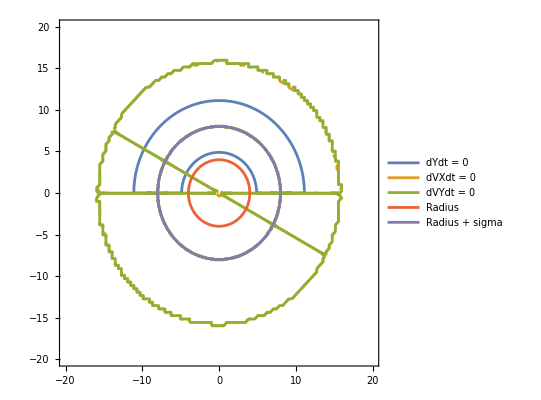

{x→-4.300142747588544,y→2.320971182180069,vely→-0.4749736834815167}

```mathematica
ClearAll[rule];
rule={
radius->4,
sigma->4,
DeflectorPushout->1,
DeflectorSigmaFactor->19/10,

u->88/100
};

ClearAll[funcs];
funcs={
vely+k0 f[radius+DeflectorPushout sigma-Sqrt[x^2+y^2],1,0,DeflectorSigmaFactor sigma] f[-radius-DeflectorPushout sigma+Sqrt[x^2+y^2],1,0,DeflectorSigmaFactor sigma] Sign[y]==0,
-1/(√(x^2+y^2))k0 vely ((-1+u^2) x+u vely y) Sign[y] (f[-radius-DeflectorPushout sigma+√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] Derivative[1,0,0,0][f][radius+DeflectorPushout sigma-√(x^2+y^2),1,0,DeflectorSigmaFactor sigma]-f[radius+DeflectorPushout sigma-√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] Derivative[1,0,0,0][f][-radius-DeflectorPushout sigma+√(x^2+y^2),1,0,DeflectorSigmaFactor sigma])==0,
-1/(√(x^2+y^2))k0 vely (u vely x+(-1+vely^2) y) Sign[y] (f[-radius-DeflectorPushout sigma+√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] Derivative[1,0,0,0][f][radius+DeflectorPushout sigma-√(x^2+y^2),1,0,DeflectorSigmaFactor sigma]-f[radius+DeflectorPushout sigma-√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] Derivative[1,0,0,0][f][-radius-DeflectorPushout sigma+√(x^2+y^2),1,0,DeflectorSigmaFactor sigma])==0
}//.rule;

ClearAll[f];
f[x_,y0_,x0_,dx_]=CInfTransition[x,y0,x0,dx];

ClearAll[funcsPlot];
funcsPlot=Join[
Simplify[funcs//.{vely->-Sqrt[1-(88/100)^2],k0->70/100}],
{Sqrt[x^2+y^2]==radius,Sqrt[x^2+y^2]==radius+sigma}//.rule
];

ContourPlot[
funcsPlot,
{x,-20,20},
{y,-20,20},
Exclusions->None,
PlotPoints->100,
PlotLegends->{
"dYdt = 0",
"dVXdt = 0",
"dVYdt = 0",
"Radius",
"Radius + sigma"
}
]

FindRoot[
funcs//.k0->7/10,
{x,-4},
{y,4},
{vely,-1/2},
AccuracyGoal->10,
PrecisionGoal->10,
WorkingPrecision->16
]

ClearAll[funcsPlot];
ClearAll[f];
ClearAll[funcs];
ClearAll[rule];
```